```mathematica
Quit[]
```

```mathematica
mZ=91.16;
mW=79.82;
v=246;
g2=√((4mW^2)/v^2);
g1=√((4mZ^2)/v^2-g2^2);
mμ=0.10566;
(*gZ=(4mZ^2)/v^2;*)
gZ=(2mZ)/v;(*definicion de la tesis gZ=Sqrt[g1^2+g2^2]*)
el=(g1 g2)/(√(g2^2+g1^2));
 sinsqW=0.223;

xi[BRinv_,zchi_]:=Sqrt[(3BRinv-1)/((1-BRinv)*2Sqrt[1-4zchi]*(1+2zchi) )]
tμZpgam[Qμ_]:=(2 Qμ)(-1/2+2 sinsqW)(-1);
tμZpZ[Qμ_]:=(2 Qμ)((-1/2+2 sinsqW)^2+(-1/2)^2);
(*tνμZpZ[Qμ_]:=( Qμ)((1/2)^2+(1/2)^2);*)
tνμZpZ[Qμ_]:=( Qμ)((1/2)^2+(1/2)^2+2(1/2)^2);(*es igual a 4 Qmu (1/2)(1/2) coincidiendo con la tesis*)
```

```mathematica
(* mumu check*)
σmumu[mZp_, BRinv_] := (12*Pi*mZp^2)/((mZp^2-(2mμ)^2)*mZp^2)*(1-BRinv)^2*1/(2.568 10^(-9))
```

```mathematica
σmumu[200, 0.65] //ScientificForm
```

σmumu[200,6.5×10^-1]

```mathematica
tμZpZ[1]
```

0.505832

```mathematica
gZ
```

0.741138

```mathematica
g2
g1
```

0.648943

0.357993

```mathematica
0.6489430894308942
```

0.648943

```mathematica
I3[p2_,q2_, pq_,mf_]:=-NIntegrate[(x y)/(y(1-y)p2+x(1-x)q2+2 x y pq-mf^2),{x,0,1},{y,0,1-x}];
I4[p2_,q2_, pq_,mf_]:=NIntegrate[(x(x-1))/(y(1-y)p2+x(1-x)q2+2 x y pq-mf^2),{x,0,1},{y,0,1-x}];
I5[p2_,q2_, pq_,mf_]:=-NIntegrate[(y(y-1))/(y(1-y)p2+x(1-x)q2+2 x y pq-mf^2),{x,0,1},{y,0,1-x}];
I6[p2_,q2_, pq_,mf_]:=NIntegrate[(x y)/(y(1-y)p2+x(1-x)q2+2 x y pq-mf^2),{x,0,1},{y,0,1-x}];
I0[p2_,q2_, pq_,mf_]:=-NIntegrate[1/(y(1-y)p2+x(1-x)q2+2 x y pq-mf^2),{x,0,1},{y,0,1-x}];
```

```mathematica
I3[s_,mZp_, mf_]:=-NIntegrate[(x y)/(y(1-y)s^2+x(1-x)mZ^2+ x y (s^2+mZ^2-mZp^2)-mf^2),{x,0,1},{y,0,1-x}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.366579,0.264972}. NIntegrate obtained -1.15649×10^-6 and 0.0000202353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.631595,0.264263}. NIntegrate obtained -0.0000369922 and 0.000015759 for the integral and error estimates.

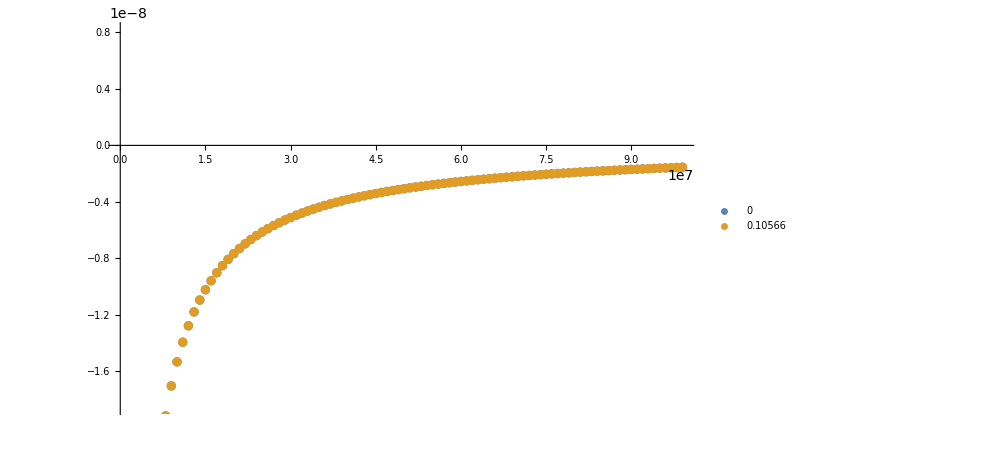

```mathematica
ListPlot[Table[{s,I3[s,200,m]},{m,{0,mμ}},{s,10^2,10000^2,10^6}], PlotLegends->{0,mμ}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

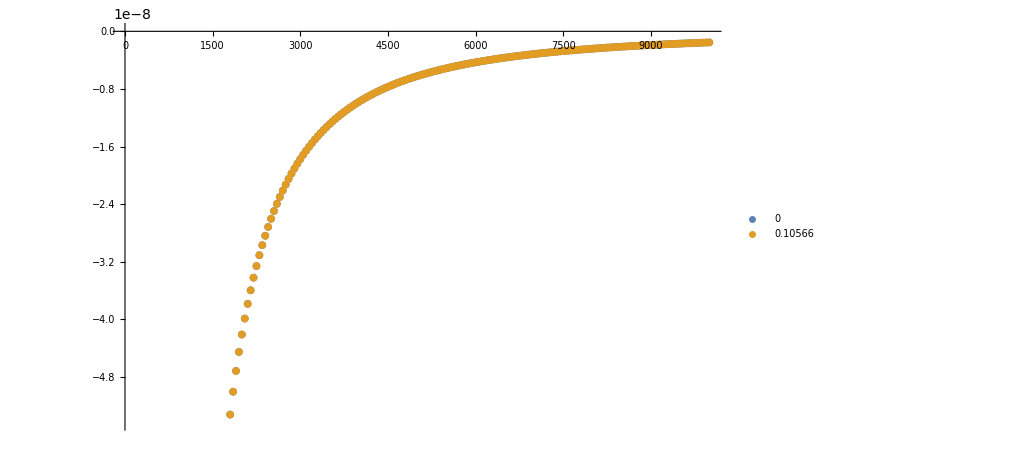

```mathematica
ListPlot[Table[{s,I3[s,1000,m]},{m,{0,mμ}},{s,1100,10000,50}], PlotLegends->{0,mμ}]
```

```mathematica
I4[s_,mZp_, mf_]:=NIntegrate[(x(x-1))/(y(1-y)s^2+x(1-x)mZ^2+ x y (s^2+mZ^2-mZp^2)-mf^2),{x,0,1},{y,0,1-x}];
```

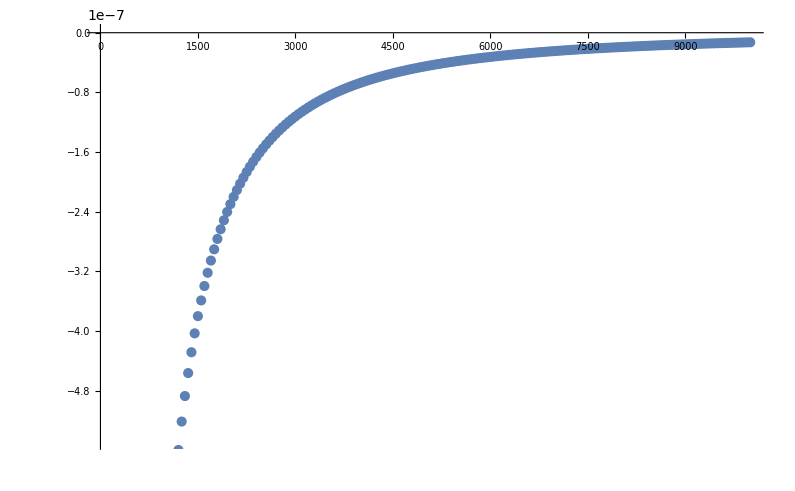

```mathematica
ListPlot[Table[{s,I4[s,200,0]},{s,300,10000,50}]]
```

```mathematica
I5[s_,mZp_, mf_]:=-NIntegrate[(y(y-1))/(y(1-y)s^2+x(1-x)mZ^2+ x y (s^2+mZ^2-mZp^2)-mf^2),{x,0,1},{y,0,1-x}];
```

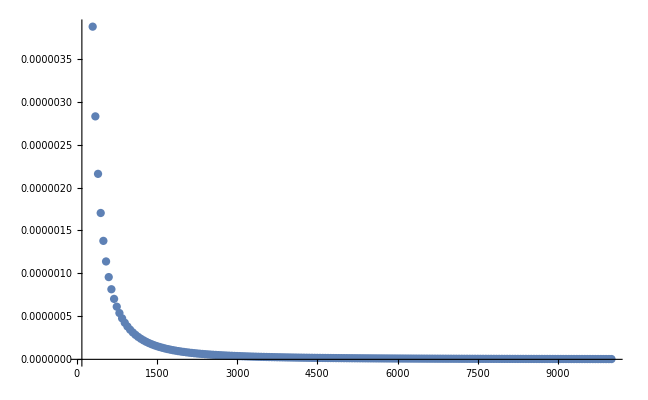

```mathematica
ListPlot[Table[{s,I5[s,200,0]},{s,300,10000,50}],PlotRange->All]
```

```mathematica
PrintParamCardZZp[mZp_, sqrts_]:=Module[{p2, q2, pq},
p2 =sqrts^2;
q2 = mZ^2;
pq =( mZp^2-sqrts^2-mZ^2)/2;
Print[
"      4 ",NumberForm[I3[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]," # i3zzmu \n",
"      5 ",NumberForm[I4[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zzmu \n","      6 ",NumberForm[I5[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zzmu \n","      7 ",NumberForm[I6[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zzmu \n","      8 ",NumberForm[I0[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zzmu \n","      9 ",NumberForm[I3[p2,q2,pq,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i3zznumu \n","      10 ",NumberForm[I4[p2,q2,pq,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zznumu \n","      11 ",NumberForm[I5[p2,q2,pq,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zznumu \n","      12 ",NumberForm[I6[p2,q2,pq,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zznumu \n","      13 ",NumberForm[I0[p2,q2,pq,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zznumu \n","      14 ",NumberForm[I3[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i3zgammamu \n","      15 ",NumberForm[I4[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i4zgammamu \n","      16 ",NumberForm[I5[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i5zgammamu \n","      17 ",NumberForm[I6[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i6zgammamu \n","      18 ",NumberForm[I0[p2,q2,pq,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i0zgammamu\n", "      19 ", NumberForm[p2,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pZZsqr\n",
"      20 ", NumberForm[q2,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # qZZsqr\n",
"      21 ", NumberForm[pq,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pqZZ\n",
"      22 ", NumberForm[p2,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pZAsqr\n",
"      23 ", NumberForm[q2,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # qZAsqr\n",
"      24 ", NumberForm[pq,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pqZA\n",
"###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 ", 
 NumberForm[mZp,{3,6},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]," # mzpmu"]]
```

```mathematica
PrintParamCardZZp[380., 1000000.]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999890804242600211871438281845819728843594020872842520475387573,0.00164136}. NIntegrate obtained 2.9586×10^-10 and 9.40541×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999890804242600211871438281845819728843594020872842520475387573,0.00164136}. NIntegrate obtained 2.9586×10^-10 and 9.40541×10^-12 for the integral and error estimates.

4 -7.3753503110e-12 # i3zzmu 
      5 -1.6178236520e-11 # i4zzmu 
      6 7.8753492120e-12 # i5zzmu 
      7 7.3753503110e-12 # i6zzmu 
      8 -2.9586047370e-10 # i0zzmu 
      9 -7.3753493030e-12 # i3zznumu 
      10 -1.6178218240e-11 # i4zznumu 
      11 7.8753482030e-12 # i5zznumu 
      12 7.3753493030e-12 # i6zznumu 
      13 -2.9634370580e-10 # i0zznumu 
      14 -7.3753503110e-12 # i3zgammamu 
      15 -1.6178236520e-11 # i4zgammamu 
      16 7.8753492120e-12 # i5zgammamu 
      17 7.3753503110e-12 # i6zgammamu 
      18 -2.9586047370e-10 # i0zgammamu
      19 1.0000000000e12 # pZZsqr
      20 8.3101456000e3 # qZZsqr
      21 -4.9999993200e11 # pqZZ
      22 1.0000000000e12 # pZAsqr
      23 8.3101456000e3 # qZAsqr
      24 -4.9999993200e11 # pqZA
###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 3.800000e2 # mzpmu

```mathematica
PrintParamCardZV[mZp_,sqrts_]:=Module[{p2ZZ, q2ZZ, pqZZ, p2ZA, q2ZA, pqZA },
p2ZZ =mZ^2;
q2ZZ = mZ^2;
pqZZ =( sqrts^2-2mZ^2)/2;
p2ZA =mZ^2;
q2ZA = 0.;
pqZA =( sqrts^2-mZ^2)/2;
Print[
"      4 ",NumberForm[I3[p2ZZ,q2ZZ,pqZZ,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]," # i3zzmu \n",
"      5 ",NumberForm[I4[p2ZZ,q2ZZ,pqZZ,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zzmu \n","      6 ",NumberForm[I5[p2ZZ,q2ZZ,pqZZ,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zzmu \n","      7 ",NumberForm[I6[p2ZZ,q2ZZ,pqZZ,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zzmu \n","      8 ",NumberForm[I0[p2ZZ,q2ZZ,pqZZ,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zzmu \n","      9 ",NumberForm[I3[p2ZZ,q2ZZ,pqZZ,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i3zznumu \n","      10 ",NumberForm[I4[p2ZZ,q2ZZ,pqZZ,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zznumu \n","      11 ",NumberForm[I5[p2ZZ,q2ZZ,pqZZ,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zznumu \n","      12 ",NumberForm[I6[p2ZZ,q2ZZ,pqZZ,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zznumu \n","      13 ",NumberForm[I0[p2ZZ,q2ZZ,pqZZ,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zznumu \n","      14 ",NumberForm[I3[p2ZA,q2ZA,pqZA,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i3zgammamu \n","      15 ",NumberForm[I4[p2ZA,q2ZA,pqZA,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i4zgammamu \n","      16 ",NumberForm[I5[p2ZA,q2ZA,pqZA,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i5zgammamu \n","      17 ",NumberForm[I6[p2ZA,q2ZA,pqZA,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i6zgammamu \n","      18 ",NumberForm[I0[p2ZA,q2ZA,pqZA,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i0zgammamu\n", "      19 ", NumberForm[p2ZZ,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pZZsqr\n",
"      20 ", NumberForm[q2ZZ,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # qZZsqr\n",
"      21 ", NumberForm[pqZZ,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pqZZ\n",
"      22 ", NumberForm[p2ZA,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pZAsqr\n",
"      23 ", NumberForm[q2ZA,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # qZAsqr\n",
"      24 ", NumberForm[pqZA,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # pqZA\n",
"###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 ", 
 NumberForm[mZp,{3,6},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]," # mzpmu"]]
```

```mathematica
PrintParamCardZV[200.,200.]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000172242,0.249391}. NIntegrate obtained 0.000153981 and 1.29276×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.74097,1.3455×10^-6}. NIntegrate obtained 9.27638×10^-6 and 3.1524×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.372564,8.84555×10^-7}. NIntegrate obtained -0.000127897 and 0.0000295176 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

4 -7.4332132220e-6 # i3zzmu 
      5 -1.9627532910e-5 # i4zzmu 
      6 1.9627534630e-5 # i5zzmu 
      7 7.4332132220e-6 # i6zzmu 
      8 -1.5398123610e-4 # i0zzmu 
      9 -7.4331943480e-6 # i3zznumu 
      10 -1.9627455900e-5 # i4zznumu 
      11 1.9627457770e-5 # i5zznumu 
      12 7.4331943480e-6 # i6zznumu 
      13 -1.5397828380e-4 # i0zznumu 
      14 -9.2763768820e-6 # i3zgammamu 
      15 -1.2789676550e-4 # i4zgammamu 
      16 2.4793879480e-5 # i5zgammamu 
      17 9.2763768820e-6 # i6zgammamu 
      18 -9.3382691980e-4 # i0zgammamu
      19 8.3101456000e3 # pZZsqr
      20 8.3101456000e3 # qZZsqr
      21 1.1689854400e4 # pqZZ
      22 8.3101456000e3 # pZAsqr
      23 0.0000000000e0 # qZAsqr
      24 1.5844927200e4 # pqZA
###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 2.000000e2 # mzpmu

```mathematica
(* Z' interno off shell *)
```

```mathematica
pF1[mZp_]:= mZp/2(1-mZ^2/mZp^2);
p1q1[sqrts_]:=1/2(sqrts^2-mZ^2);
pF2[mZp_]:= mZp/2 √(1-(4mZ^2)/mZp^2);
p2q2[sqrts_]:=1/2(sqrts^2-2*mZ^2);
```

```mathematica
I3[mZp_,mf_,sqrts_]:=-NIntegrate[(x y)/(y(1-y)mZ^2+2 x y p1q1[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I4[mZp_,mf_,sqrts_]:=NIntegrate[(x(x-1))/(y(1-y)mZ^2+2 x y p1q1[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I5[mZp_,mf_,sqrts_]:=-NIntegrate[(y(y-1))/(y(1-y)mZ^2+2 x y p1q1[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I6[mZp_,mf_,sqrts_]:=NIntegrate[(x y)/(y(1-y)mZ^2+2 x y p1q1[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I0[mZp_,mf_,sqrts_]:=-NIntegrate[1/(y(1-y)mZ^2+2 x y p1q1[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
```

```mathematica
I33[mZp_,mf_,sqrts_]:=-NIntegrate[(x y)/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I44[mZp_,mf_, sqrts_]:=NIntegrate[(x(x-1))/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I55[mZp_,mf_, sqrts_]:=-NIntegrate[(y(y-1))/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I66[mZp_,mf_, sqrts_]:=NIntegrate[(x y)/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
I00[mZp_,mf_, sqrts_]:=-NIntegrate[1/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[sqrts]-mf^2),{x,0,1},{y,0,1-x}];
```

```mathematica
PrintForParamCard[mZp_, sqrts_]:=Print["      4 ",NumberForm[I33[mZp,mμ,sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i3zzmu \n","      5 ",NumberForm[I44[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zzmu \n","      6 ",NumberForm[I55[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zzmu \n","      7 ",NumberForm[I66[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zzmu \n","      8 ",NumberForm[I00[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zzmu \n","      9 ",NumberForm[I33[mZp,0, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i3zznumu \n","      10 ",NumberForm[I44[mZp,0, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zznumu \n","      11 ",NumberForm[I55[mZp,0, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zznumu \n","      12 ",NumberForm[I66[mZp,0, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zznumu \n","      13 ",NumberForm[I00[mZp,0, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zznumu \n","      14 ",NumberForm[I3[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i3zgammamu \n","      15 ",NumberForm[I4[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i4zgammamu \n","      16 ",NumberForm[I5[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i5zgammamu \n","      17 ",NumberForm[I6[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i6zgammamu \n","      18 ",NumberForm[I0[mZp,mμ, sqrts],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i0zgammamu\n", "      19 ", NumberForm[sqrts,{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # sqrts\n",
"###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 ", 
 NumberForm[mZp,{3,6},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]," # mzpmu"]
```

```mathematica
PrintForParamCard[380.,90.]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.9999986509658627148360063687567572676684335419849958270788192749,0.163454}. NIntegrate obtained 0.000284473 and 2.57105×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.849305,9.07055×10^-6}. NIntegrate obtained 0.0000306016 and 7.0319×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.49097,2.65829×10^-6}. NIntegrate obtained -0.000248152 and 0.0000810381 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

4 -2.0335263900e-5 # i3zzmu 
      5 -4.0508630700e-5 # i4zzmu 
      6 4.0508636270e-5 # i5zzmu 
      7 2.0335263900e-5 # i6zzmu 
      8 -2.8447318540e-4 # i0zzmu 
      9 -2.0335133830e-5 # i3zznumu 
      10 -4.0508372770e-5 # i4zznumu 
      11 4.0508418450e-5 # i5zznumu 
      12 2.0335133830e-5 # i6zznumu 
      13 -2.8446628990e-4 # i0zznumu 
      14 -3.0601594710e-5 # i3zgammamu 
      15 -2.4815175900e-4 # i4zgammamu 
      16 6.0943421250e-5 # i5zgammamu 
      17 3.0601594710e-5 # i6zgammamu 
      18 -1.6158934060e-3 # i0zgammamu
      19 9.0000000000e1 # sqrts
###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 3.800000e2 # mzpmu

```mathematica
(* Z' interno on shell*)
```

```mathematica
pF1[mZp_]:= mZp/2(1-mZ^2/mZp^2);
p1q1[mZp_]:=pF1[mZp] √(mZ^2+pF1[mZp]^2)+pF1[mZp]^2;
pF2[mZp_]:= mZp/2 √(1-(4mZ^2)/mZp^2);
p2q2[mZp_]:=+(mZ^2+2pF2[mZp]^2);
```

```mathematica
I3[mZp_,mf_]:=-NIntegrate[(x y)/(y(1-y)mZ^2+2 x y p1q1[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I4[mZp_,mf_]:=NIntegrate[(x(x-1))/(y(1-y)mZ^2+2 x y p1q1[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I5[mZp_,mf_]:=-NIntegrate[(y(y-1))/(y(1-y)mZ^2+2 x y p1q1[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I6[mZp_,mf_]:=NIntegrate[(x y)/(y(1-y)mZ^2+2 x y p1q1[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I0[mZp_,mf_]:=-NIntegrate[1/(y(1-y)mZ^2+2 x y p1q1[mZp]-mf^2),{x,0,1},{y,0,1-x}];
```

```mathematica
I33[mZp_,mf_]:=-NIntegrate[(x y)/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I44[mZp_,mf_]:=NIntegrate[(x(x-1))/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I55[mZp_,mf_]:=-NIntegrate[(y(y-1))/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I66[mZp_,mf_]:=NIntegrate[(x y)/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[mZp]-mf^2),{x,0,1},{y,0,1-x}];
I00[mZp_,mf_]:=-NIntegrate[1/((x(1-x)+y(1-y))mZ^2+2 x y p2q2[mZp]-mf^2),{x,0,1},{y,0,1-x}];
```

```mathematica
pathIntegrales="/media/santi/HDD/V/Doctorado/Zpmu/muon_collider/events_anomalies/0_param_cards/integrales/";
```

```mathematica
masaIn = 190;
masaFin = 1000;
intervaloMasa = 10;
Export[pathIntegrales<>"todo.csv", Table[{m,I33[m,mμ], I44[m,mμ],I55[m,mμ],I66[m,mμ],I00[m,mμ],I33[m,0],I44[m,0],I55[m,0],I66[m,0],I00[m,0],I3[m,mμ],I4[m,mμ],I5[m,mμ],I6[m,mμ],I0[m,mμ]}, {m,masaIn,masaFin,intervaloMasa}], "CSV"];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000172242,0.249391}. NIntegrate obtained 0.000161019 and 1.32351×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.427758,9.5938×10^-7}. NIntegrate obtained 0.0000100897 and 8.62867×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.427758,9.5938×10^-7}. NIntegrate obtained -0.000123243 and 0.0000771184 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
PrintForParamCard[mZp_]:=Print["      4 ",NumberForm[I33[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i3zzmu \n","      5 ",NumberForm[I44[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zzmu \n","      6 ",NumberForm[I55[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zzmu \n","      7 ",NumberForm[I66[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zzmu \n","      8 ",NumberForm[I00[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zzmu \n","      9 ",NumberForm[I33[mZp,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i3zznumu \n","      10 ",NumberForm[I44[mZp,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i4zznumu \n","      11 ",NumberForm[I55[mZp,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i5zznumu \n","      12 ",NumberForm[I66[mZp,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i6zznumu \n","      13 ",NumberForm[I00[mZp,0],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)], " # i0zznumu \n","      14 ",NumberForm[I3[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i3zgammamu \n","      15 ",NumberForm[I4[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i4zgammamu \n","      16 ",NumberForm[I5[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i5zgammamu \n","      17 ",NumberForm[I6[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i6zgammamu \n","      18 ",NumberForm[I0[mZp,mμ],{10,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)],  " # i0zgammamu\n", 
"###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 ", 
 NumberForm[mZp,{3,6},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]," # mzpmu"]
```

```mathematica
NumberForm[200.0,{3,6},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]
```

2.000000e2

```mathematica
PrintForParamCard[380.]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000827045 and 8.72614×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.495129,2.91716×10^-7}. NIntegrate obtained -0.0000477234 and 9.03281×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0145079,1.11523×10^-6}. NIntegrate obtained -0.0000104899 and 2.47939×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

4 -2.7103759650e-6 # i3zzmu 
      5 -9.2459216570e-6 # i4zzmu 
      6 9.2459204930e-6 # i5zzmu 
      7 2.7103759650e-6 # i6zzmu 
      8 -8.2704465000e-5 # i0zzmu 
      9 -2.7103725870e-6 # i3zznumu 
      10 -9.2458920780e-6 # i4zznumu 
      11 9.2458909180e-6 # i5zznumu 
      12 2.7103725870e-6 # i6zznumu 
      13 -8.2702139540e-5 # i0zznumu 
      14 -3.0335049460e-6 # i3zgammamu 
      15 -4.7723447100e-5 # i4zgammamu 
      16 1.0489897410e-5 # i5zgammamu 
      17 3.0335049460e-6 # i6zgammamu 
      18 -3.4206150520e-4 # i0zgammamu
###################################
## INFORMATION FOR MASS
###################################
BLOCK MASS # 
      1 5.040000e-03 # md
      2 2.550000e-03 # mu
      3 1.010000e-01 # ms
      4 1.270000e+00 # mc
      5 4.700000e+00 # mb
      6 1.720000e+02 # mt
      11 5.110000e-04 # me
      13 1.056600e-01 # mmu
      15 1.777000e+00 # mta
      23 9.118760e+01 # mz
      25 1.250000e+02 # mh
      101 2.000000e+01 # mch
      102 3.800000e2 # mzpmu

```mathematica
Print[NumberForm[I33[mZp,mμ],{5,10},ExponentFunction->(#&),NumberFormat->(SequenceForm[#1,"e",#3]&)]]
```

-1.6854000000e-6

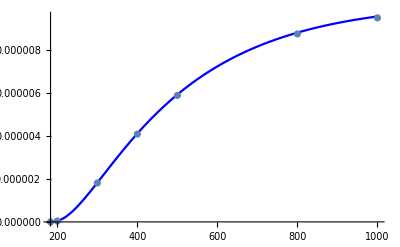

```mathematica
Show[{Plot[GamZpZZ[mZp,1,1],{mZp,183,1000},PlotStyle->Blue],ListPlot[{{183, 1.2099*^-11},{200,4.1632*^-8}, {300, 1.8099*^-6},{400, 4.0834*^-6}, {500, 5.884*^-6},{800,8.7451*^-6}, {1000, 9.4926*^-6}}]},PlotRange->All]
```

```mathematica
GamZpZZ[183,1,1]
```

1.50462×10^-11

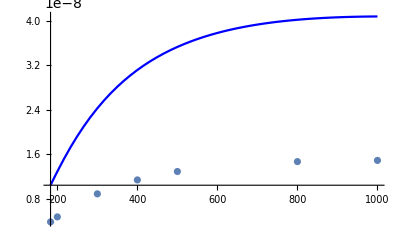

```mathematica
Show[{Plot[GamZpZgam[mZp,1,1],{mZp,183,1000},PlotStyle->Blue],ListPlot[{{183, 3.7862*^-9},{200,4.6885*^-9}, {300, 8.8411*^-9},{400, 1.1354*^-8}, {500, 1.2869*^-8},{800,1.4653*^-8}, {1000, 1.4869*^-8}}]},PlotRange->All]
```

```mathematica
GamZpZgam[200,1,1]
```

1.28736×10^-8

```mathematica
BRZZ[500,1,1,0.65]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000612749 and 8.40076×10^-10 for the integral and error estimates.

1.56356×10^-7

```mathematica
GamZpZZ[500,1,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000612749 and 8.40076×10^-10 for the integral and error estimates.

5.92496×10^-6

```mathematica
xi[0.65,0.01]
```

1.16532

```mathematica
(1-4*mZ^2/200^2)^(3/2)/(1-4*mZ^2/500^2)^(3/2) *0.003187
```

0.00027422

```mathematica
GamTot[mZp_,gZp_,Qμ_,BRinv_]:= (mZp*(Qμ*gZp)^2)/(12Pi*(1-BRinv)) ;
GamZpμμ[mZp_,gZp_,Qμ_]:=((gZp*Qμ)^2*mZp)/(12*Pi)*(1-4(mμ/mZ)^2)^(3/2);
```

```mathematica
AZpZZsqI0Zero[mZp_,gZp_,Qμ_]:=(gZp^2 gZ^4)/(192 π^4 mZ^2)(mZp^2-4mZ^2)^2(tμZpZ[Qμ] mZ^2(I33[mZp,mμ]+I55[mZp,mμ])+tνμZpZ[Qμ] mZ^2(I33[mZp,0]+I55[mZp,0]))^2;
GamZpZZI0Zero[mZp_,gZp_,Qμ_]:=1/2 pF2[mZp]/(32 π^2 mZp^2)4π AZpZZsqI0Zero[mZp,gZp,Qμ];
BRZZI0Zero[mZp_,gZp_,Qμ_,BrInv_]:=(1/2 pF2[mZp]/(32 π^2 mZp^2)4π AZpZZsqI0Zero[mZp,gZp,Qμ])/(gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv))));
σμμtoZtoZZI0Zero[mZp_,gZp_,Qμ_,BrInv_]:=((12 π (1-BrInv) BRZZI0Zero[mZp,gZp,Qμ,BrInv])/(mZp^2-4mZ^2))1/(2.568 10^(-9))10^3;
```

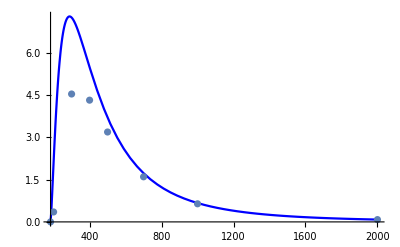

```mathematica
Show[{Plot[σμμtoZtoZZI0Zero[mZp,1,1,0.65],{mZp,183,2000},PlotStyle->Blue],ListPlot[{{183,1.339*^-4},{200,0.3529}, {300, 4.544},{400, 4.325},{500,3.194}, {700,1.602}, {1000,0.6433}, {2000,0.08186}}]},PlotRange->All]
```

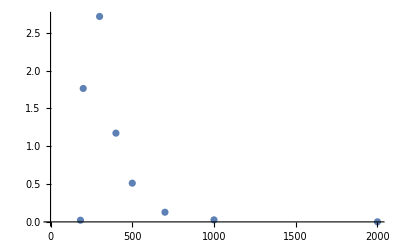

```mathematica
ListPlot[{{183,σμμtoZtoZZI0Zero[183,1,1,0.65]-1.339*^-4},{200,σμμtoZtoZZI0Zero[200,1,1,0.65]-0.3529}, {300, σμμtoZtoZZI0Zero[300,1,1,0.65]-4.544},{400,σμμtoZtoZZI0Zero[400,1,1,0.65]- 4.325},{500,σμμtoZtoZZI0Zero[500,1,1,0.65]-3.194}, {700,σμμtoZtoZZI0Zero[700,1,1,0.65]-1.602}, {1000,σμμtoZtoZZI0Zero[1000,1,1,0.65]-0.6433}, {2000,σμμtoZtoZZI0Zero[2000,1,1,0.65]-0.08186}}]
```

```mathematica
AZpgamsqI0Zero[mZp_,gZp_,Qμ_]:=(gZp^2 gZ^2 el^2)/(96 π^4 mZ^2 mZp^2)(mZp^2-mZ^2)^2(mZp^2+mZ^2)(tμZpgam[Qμ] (mZ^2(I3[mZp,mμ]+I5[mZp,mμ])))^2;
GamZpZgamI0Zero[mZp_,gZp_,Qμ_]:=pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsqI0Zero[mZp,gZp,Qμ];
BRZgamI0Zero[mZp_,gZp_,Qμ_,BrInv_]:=(pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsqI0Zero[mZp,gZp,Qμ])/(gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv))));
σμμtoZtoZγI0Zero[mZp_,gZp_,Qμ_,BrInv_]:=((12 π mZp^2 (1-BrInv)  BRZgamI0Zero[mZp,gZp,Qμ,BrInv])/((mZp^2-mZ^2)^2))1/(2.568 10^(-9))10^3
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.714539,4.09787×10^-6}. NIntegrate obtained 0.0000265275 and 3.13244×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.0115456,1.35016×10^-6}. NIntegrate obtained -0.0000547503 and 4.76326×10^-10 for the integral and error estimates.

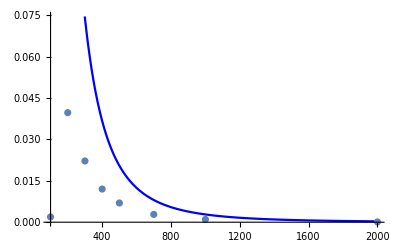

```mathematica
Show[{Plot[σμμtoZtoZγI0Zero[mZp,1,1,0.65],{mZp,100,2000},PlotStyle->Blue],ListPlot[{{100,1.921*^-3},{200,3.973*^-2}, {300, 2.221*^-2},{400, 1.203*^-2},{500,6.978*^-3}, {700,2.837*^-3}, {1000,1.009*^-3}, {2000,1.158*^-4}}]},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.713879,3.95963×10^-6}. NIntegrate obtained 0.0000265417 and 2.49314×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.713879,3.95963×10^-6}. NIntegrate obtained -0.0000547723 and 4.60524×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.74097,1.3455×10^-6}. NIntegrate obtained 9.27638×10^-6 and 3.1524×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

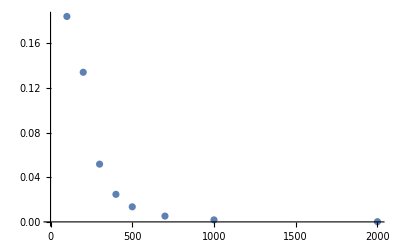

```mathematica
ListPlot[{{100,σμμtoZtoZγI0Zero[100,1,1,0.65]-1.921*^-3},{200,σμμtoZtoZγI0Zero[200,1,1,0.65]-3.973*^-2}, {300,σμμtoZtoZγI0Zero[300,1,1,0.65]- 2.221*^-2},{400,σμμtoZtoZγI0Zero[400,1,1,0.65]-1.203*^-2},{500,σμμtoZtoZγI0Zero[500,1,1,0.65]-6.978*^-3}, {700,σμμtoZtoZγI0Zero[700,1,1,0.65]-2.837*^-3}, {1000,σμμtoZtoZγI0Zero[1000,1,1,0.65]-1.009*^-3}, {2000,σμμtoZtoZγI0Zero[2000,1,1,0.65]-1.158*^-4}}]
```

```mathematica
AZpgamsqI0Zero[mZp_,gZp_,Qμ_]:=(gZp^2 gZ^2 el^2)/(96 π^4 mZ^2 mZp^2)(mZp^2-mZ^2)^2(mZp^2+mZ^2)(tμZpgam[Qμ] (mZ^2(I3[mZp,mμ]+I5[mZp,mμ])))^2;
GamZpZgamI0Zero[mZp_,gZp_,Qμ_]:=pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsqI0Zero[mZp,gZp,Qμ];
BRZgamI0Zero[mZp_,gZp_,Qμ_,BrInv_]:=(pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsqI0Zero[mZp,gZp,Qμ])/(gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv))));
σμμtoZtoZγI0Zero[mZp_,gZp_,Qμ_,BrInv_]:=((12 π mZp^2 (1-BrInv)  BRZgamI0Zero[mZp,gZp,Qμ,BrInv])/((mZp^2-mZ^2)^2))1/(2.568 10^(-9))10^3
```

```mathematica
AZpgamsqA6[mZp_,gZp_,Qμ_]:=(gZp^2 gZ^2 el^2)/(384π^4 mZ^2)(mZp^2-mZ^2)^4(tμZpgam[Qμ] I6[mZp,mμ])^2;
GamZpZgamA6[mZp_,gZp_,Qμ_]:=pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsqA6[mZp,gZp,Qμ];
BRZgamA6[mZp_,gZp_,Qμ_,BrInv_]:=(pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsqA6[mZp,gZp,Qμ])/(gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv))));
σμμtoZtoZγA6[mZp_,gZp_,Qμ_,BrInv_]:=((12 π mZp^2 (1-BrInv)  BRZgamA6[mZp,gZp,Qμ,BrInv])/((mZp^2-mZ^2)^2))1/(2.568 10^(-9))10^3
```

```mathematica
GamZpZgamA6[1000,1,1]
```

3.0169×10^-6

```mathematica
F[σ_,Γ_,mZp_,gZp_,Qμ_]:=(σ *2.568*^-9)/(12Pi)*(mZp^2-4*mZ^2)*Γ^2/GamZpμμ[mZp,gZp,Qμ];
```

```mathematica
GamTot[300,1,1,0.65]
```

22.7364

```mathematica
σμμtoZtoZZI0Zero[200,1,1,0.65]
```

2.11762

```mathematica
GamZpZZI0Zero[200,1,1]
```

4.22264×10^-8

```mathematica
F[2.1176183720957287,15.1576 ,200,1,1]
```

0.0000422266

```mathematica
F[0.00035263,15.15762 ,200,1,1]
```

7.03168×10^-9

```mathematica
AZpgamsq[mZp_,gZp_,Qμ_]:=(gZp^2 gZ^2 el^2)/(96 π^4 mZ^2 mZp^2)(mZp^2-mZ^2)^2(mZp^2+mZ^2)(tμZpgam[Qμ] (mZ^2(I3[mZp,mμ]+I5[mZp,mμ])+mμ^2 I0[mZp,mμ]))^2;
```

```mathematica
AZpZZsq[mZp_,gZp_,Qμ_]:=(gZp^2 gZ^4)/(192 π^4 mZ^2)(mZp^2-4mZ^2)^2(tμZpZ[Qμ] mZ^2(I33[mZp,mμ]+I55[mZp,mμ])+tνμZpZ[Qμ] mZ^2(I33[mZp,0]+I55[mZp,0])+tμZpZ[Qμ] mμ^2 I00[mZp,mμ])^2;
```

```mathematica
GamZpZgam[mZp_,gZp_,Qμ_]:=pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsq[mZp,gZp,Qμ];
GamZpZZ[mZp_,gZp_,Qμ_]:=1/2 pF2[mZp]/(32 π^2 mZp^2)4π AZpZZsq[mZp,gZp,Qμ];

BrInv[ξ_,z_]:= (1+2 ξ^2(1-4 z)^(1/2)(1+2z))/(3+2ξ^2(1-4z)^(1/2)(1+2 z));
Br2mu[ξ_,z_]:=1-BrInv[ξ,z];
GamTot[mZp_,gZp_,Qμ_,ξ_,z_]:=gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv[ξ,z]-1)/(24 π(1-BrInv[ξ,z])));
BRZgam[mZp_,gZp_,Qμ_,BrInv_]:=(pF1[mZp]/(32 π^2 mZp^2)4π AZpgamsq[mZp,gZp,Qμ])/(gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv))));
```

```mathematica
BrInv[1.165,0.01]
```

0.649909

```mathematica
BRZZ[mZp_,gZp_,Qμ_,BrInv_]:=(1/2 pF2[mZp]/(32 π^2 mZp^2)4π AZpZZsq[mZp,gZp,Qμ])/(gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv))));
```

```mathematica
BRZZ[200,1,1,0.65]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000172242,0.249391}. NIntegrate obtained 0.000153981 and 1.29276×10^-9 for the integral and error estimates.

2.78579×10^-9

```mathematica
GamZpZZ[200,1,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000172242,0.249391}. NIntegrate obtained 0.000153981 and 1.29276×10^-9 for the integral and error estimates.

4.22259×10^-8

```mathematica
GamTot[250,1,1,1.16,0.01]
```

18.865

```mathematica
(* Dependencia de la xsection con width? *)
```

```mathematica
0.003191/(12*Pi*500^2*13.26290837070187*5.8840886257389*10^(-06)/((500^2-(2*mZ)^2)*37.89406^2*2.568 10^(-9)))
```

3.46779×10^-6

```mathematica
0.0003526/(12*Pi*200^2*5.305155885675071*4.1632887196150656*10^(-08)/((200^2-(2*mZ)^2)*15.15762^2*2.568 10^(-9)))
```

4.22204×10^-6

```mathematica
(* cambio término GS (apéndice D) *)
```

```mathematica
tμZpZ[1]/(1/6)
```

3.03499

```mathematica
AZpZZsqGS[mZp_,gZp_,Qμ_]:=(gZp^2 gZ^4)/(192 π^4 mZ^2)(mZp^2-4mZ^2)^2(tμZpZ[Qμ] mZ^2(I33[mZp,mμ]+I55[mZp,mμ])+tνμZpZ[Qμ] mZ^2(I33[mZp,0]+I55[mZp,0])+(Qμ/6) mμ^2 I00[mZp,mμ])^2;
BRZZGS[mZp_,gZp_,Qμ_,BrInv_]:=(1/2 pF2[mZp]/(32 π^2 mZp^2)4π AZpZZsqGS[mZp,gZp,Qμ])/(gZp^2 Qμ^2 mZp(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv))));
σμμtoZtoZZGS[mZp_,gZp_,Qμ_,BrInv_]:=((12 π (1-BrInv) BRZZGS[mZp,gZp,Qμ,BrInv])/(mZp^2-4mZ^2))1/(2.568 10^(-9))10^3;
```

```mathematica
σμμtoZtoZZGS[400,1,1,0.65]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000783134 and 8.62363×10^-10 for the integral and error estimates.

5.49877

```mathematica
ListPlot[{{200,0.3526}, {250, 3.068}, {300, 4.543},{350,4.723}, {400, 4.323},{500,3.187}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000172242,0.249391}. NIntegrate obtained 0.00015397 and 1.29166×10^-9 for the integral and error estimates.

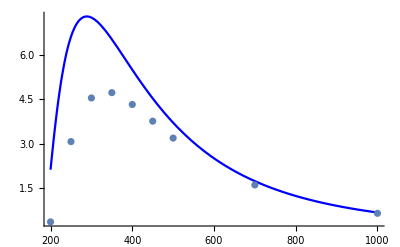

```mathematica
Show[{Plot[σμμtoZtoZZGS[mZp,1,1,0.65],{mZp,200,1000},PlotStyle->Blue],ListPlot[{{200,0.3526}, {250, 3.068}, {300, 4.543},{350,4.723}, {400, 4.323},{450, 3.759},{500,3.187}, {700,1.602}, {1000,0.643}}]},PlotRange->All]
```

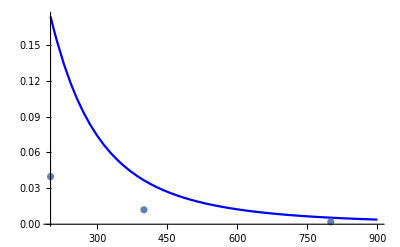

```mathematica
Show[{Plot[σμμtoZtoZγ[mZp,1,1,0.65],{mZp,200,900},PlotStyle->Blue],ListPlot[{{200, 0.03977},{400, 0.01204},{800, 0.001939}}]},PlotRange->All]
```

```mathematica
σμμtoZtoZZGS[400,1,1,0.65]/4.32
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000783134 and 8.62363×10^-10 for the integral and error estimates.

1.27286

```mathematica
σμμtoZtoZγ[400,1,1,0.65]/0.012
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0229748,9.69844×10^-7}. NIntegrate obtained -9.74925×10^-6 and 2.27596×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.372564,2.75626×10^-7}. NIntegrate obtained 0.000273086 and 0.0000816853 for the integral and error estimates.

3.06111

```mathematica
BRZZGS[500,1,1,0.65]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000612749 and 8.40076×10^-10 for the integral and error estimates.

1.56357×10^-7

```mathematica
mZp=500;
(σμμtoZtoZZGS[mZp,1,1,0.65]*GamTot[mZp,1,1,1.165320,0.01]^2*6144*Pi^5*mZ^2)/(gZ^4*(1-4*mZ^2/mZp^2)^(3/2))
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000612749 and 8.40076×10^-10 for the integral and error estimates.

3.41383×10^14

```mathematica
tμZpZ[1]
```

0.505832

```mathematica
mZp=500;
(0.0031911*37.89406^2*6144*Pi^5*mZ^2)/(gZ^4*(1-4*mZ^2/mZp^2)^(3/2))
```

2.93926×10^11

```mathematica
mZp=200;
(0.068034*15.15762^2*6144*Pi^5*mZ^2)/(gZ^4*(1-4*mZ^2/mZp^2)^(3/2))
```

1.16527×10^13

```mathematica
mZp=500;
(σμμtoZtoZZGS[mZp,1,1,0.65]*GamTot[mZp,1,1,1.165320,0.01]^2*6144*Pi^5*mZ^2)/(gZ^4*(1-4*mZ^2/mZp^2)^(3/2))
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000214327,0.0036018}. NIntegrate obtained 0.0000612749 and 8.40076×10^-10 for the integral and error estimates.

3.41383×10^14

```mathematica
mZp=500;
(0.019868*37.89407^2*6144*Pi^5*mZ^2)/(gZ^4*(1-4*mZ^2/mZp^2)^(3/2))
```

1.83×10^12

```mathematica
BRinv=0.65;
zchi = 0.01;
```

```mathematica
BRZZ[200,0.1, 1, 0.65]
```

BRZZ[200,0.1,1,0.65]

```mathematica
GamTot[200,1,1, 1.16532, 0.01]
```

15.1576

```mathematica
Sqrt[(3BRinv-1)/(2(1-BRinv)Sqrt[1-4zchi](1+2zchi))]
```

1.16532

```mathematica
BRZZ[200, 1,1,0.65]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000153981 and 1.6277×10^-9 for the integral and error estimates.

2.78579×10^-9

```mathematica
GamZpZZ[200,0.1,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000153981 and 1.6277×10^-9 for the integral and error estimates.

4.22259×10^-10

```mathematica
AZpZZsq[200,1,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000153981 and 1.6277×10^-9 for the integral and error estimates.

0.00206531

```mathematica
(tμZpZ[1] mZ^2(I33[200,mμ]+I55[200,mμ])+tνμZpZ[1] mZ^2(I33[200,0]+I55[200,0])+tμZpZ[1] mμ^2 I00[200,mμ])^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000153981 and 1.6277×10^-9 for the integral and error estimates.

0.0232851

```mathematica
tμZpZ[1] (I33[200,mμ]+I55[200,mμ])
```

6.16827×10^-6

```mathematica
GamTot[500,1*^-3,1,1.16532,0.01]//ScientificForm
```

3.78941×10^-5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.370129,7.92463×10^-7}. NIntegrate obtained 9.27588×10^-6 and 6.67656×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0265901,1.12364×10^-6}. NIntegrate obtained -0.0000247929 and 1.09783×10^-10 for the integral and error estimates.

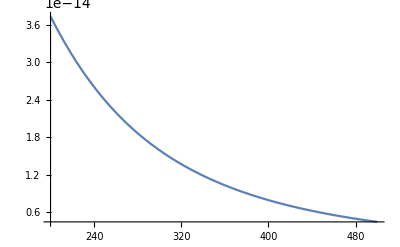

```mathematica
Plot[(mZp^2/((mZp^2-mZ^2)^2))*BRZgam[mZp,0.6,1,0.6],{mZp,200,500}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000153977 and 1.6281×10^-9 for the integral and error estimates.

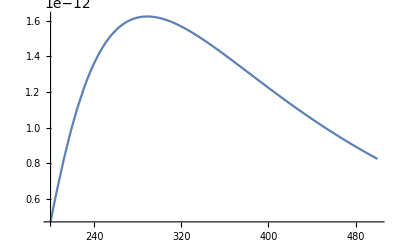

```mathematica
Plot[(1/(mZp^2-4mZ^2))*BRZZ[mZp,0.6,1,0.6],{mZp,200,500}]
```

```mathematica
(*xs en fb*)
```

```mathematica
(*σμμtoZtoZZ[mZp_,gZp_,Qμ_,ξ_,z_]:=((12 π Br2mu[ξ,z] (GamZpZZ[mZp,gZp,Qμ]/GamTot[mZp,gZp,Qμ,ξ,z]))/(mZp^2-4mZ^2))1/(2.568 10^(-9))10^3;
σμμtoZtoZγ[mZp_,gZp_,Qμ_,ξ_,z_]:=((12 π mZp^2 Br2mu[ξ,z]  (GamZpZgam[mZp,gZp,Qμ]/GamTot[mZp,gZp,Qμ,ξ,z]))/((mZp^2-mZ^2)^2))1/(2.568 10^(-9))10^3*)
```

```mathematica
σμμtoZtoZZGS[500,1,1,0.65]*2.568 10^(-9)/10^3
```

2.568×10^-12 σμμtoZtoZZGS[500,1,1,0.65]

```mathematica
σμμtoZtoZZ[mZp_,gZp_,Qμ_,BrInv_]:=((12 π (1-BrInv) BRZZ[mZp,gZp,Qμ,BrInv])/(mZp^2-4mZ^2))1/(2.568 10^(-9))10^3;
σμμtoZtoZγ[mZp_,gZp_,Qμ_,BrInv_]:=((12 π mZp^2 (1-BrInv)  BRZgam[mZp,gZp,Qμ,BrInv])/((mZp^2-mZ^2)^2))1/(2.568 10^(-9))10^3
```

```mathematica
σμμtoZtoZγ[200,1,1,0.65]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.74097,1.3455×10^-6}. NIntegrate obtained 9.27638×10^-6 and 3.1524×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0529924,1.18203×10^-6}. NIntegrate obtained -0.0000247939 and 8.41081×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.372564,8.84555×10^-7}. NIntegrate obtained 0.000933827 and 0.000214638 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.173817

```mathematica
(*σμμtoZtoZZ[mZp_,gZp_,Qμ_,ξ_,z_]:=((12 π  Br2mu[ξ,z] (GamZpZZ[mZp,gZp,Qμ]/GamTot[mZp,gZp,Qμ,ξ,z]))/(mZp^2))1/(2.568 10^(-9))10^3;
σμμtoZtoZγ[mZp_,gZp_,Qμ_,ξ_,z_]:=((12 π Br2mu[ξ,z]  (GamZpZgam[mZp,gZp,Qμ]/GamTot[mZp,gZp,Qμ,ξ,z]))/(mZp^2))1/(2.568 10^(-9))10^3*)
```

```mathematica
σμμtoZtoZZ[200,1,1,0.65]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000172242,0.249391}. NIntegrate obtained 0.000153981 and 1.29276×10^-9 for the integral and error estimates.

2.11759

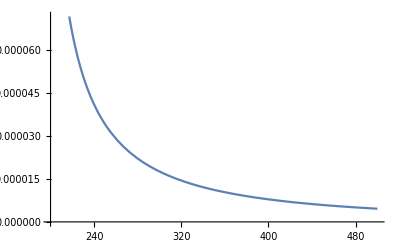

```mathematica
Plot[1/(mZp^2-4mZ^2),{mZp,200,500}]
```

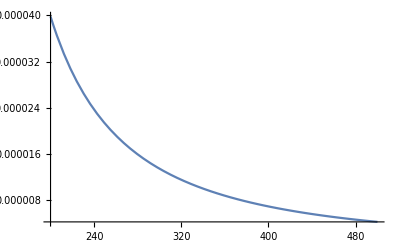

```mathematica
Plot[mZp^2/((mZp^2-mZ^2)^2),{mZp,200,500}]
```

```mathematica
(*BMI*)
```

```mathematica
xsZZtable={{"Mzp","xs [fb]"}};
Do[mZp=200.+(i-1)*50.;
xsZZ=σμμtoZtoZZ[mZp,0.6,1,0.34];
AppendTo[xsZZtable,{mZp,xsZZ}],{i,1,7}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000153981 and 1.6277×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000125685 and 1.56845×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000105372 and 1.54705×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
xsZZtable
```

{{Mzp,xs [fb]},{200.,7.53},{250.,23.5193},{300.,25.8187},{350.,23.2109},{400.,19.553},{450.,16.1012},{500.,13.1793}}

```mathematica
Export["/home/nico/Documentos/xsZZtable_BRinv_34.dat",xsZZtable]
```

/home/nico/Documentos/xsZZtable_BRinv_34.dat

```mathematica
xsZgtable={{"Mzp","xs [fb]"}};
Do[mZp=200.+(i-1)*50.;
xsZg=σμμtoZtoZγ[mZp,0.6,1,0.34];
AppendTo[xsZgtable,{mZp,xsZg}],{i,1,7}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.397829,7.93832×10^-7}. NIntegrate obtained 9.27635×10^-6 and 3.52831×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0265901,1.12364×10^-6}. NIntegrate obtained -0.0000247939 and 1.02085×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.397829,7.93832×10^-7}. NIntegrate obtained 0.000776174 and 0.000191559 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
xsZgtable
```

{{Mzp,xs [fb]},{200.,0.597136},{250.,0.381745},{300.,0.254111},{350.,0.176023},{400.,0.126187},{450.,0.0931179},{500.,0.0704199}}

```mathematica
xsZgtable
```

{{Mzp,xs [fb]},{200.,0.597064},{250.,0.381702},{300.,0.254084},{350.,0.176006},{400.,0.126173},{450.,0.0931091},{500.,0.0704132}}

```mathematica
Export["/home/nico/Documentos/xsZgtable_BRinv_34.dat",xsZgtable]
```

/home/nico/Documentos/xsZgtable_BRinv_34.dat

```mathematica
σμμtoZtoZZ[200,0.6,1,1,0.01]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000106237,0.855515}. NIntegrate obtained 0.000153981 and 1.6277×10^-9 for the integral and error estimates.

2.76719

```mathematica
(******************************************************************************************************)
(******************************************************************************************************)
(******************************************************************************************************)
(******************************************************************************************************)
(******************************************************************************************************)
(******************************************************************************************************)
(******************************************************************************************************)
```

```mathematica
ContourPlot[σμμtoZtoZZ[mZp,gp,1,1.12,0.16],{mZp,200,500},{gp,0.2,1.3}]
```

```mathematica
σμμtoZtoZγ[300,0.6,1,0.7,0.16]
σμμtoZtoZγ[400,0.6,1,0.7,0.16]
σμμtoZtoZγ[500,0.6,1,0.7,0.16]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0105023}. NIntegrate obtained -0.0000145818 and 4.36887×10^-11 for the integral and error estimates.

{0.0898871}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.0446361}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.0249096}

```mathematica
σμμtoZtoZZ[300,0.6,1,0.7,0.16]
σμμtoZtoZZ[400,0.6,1,0.7,0.16]
σμμtoZtoZZ[500,0.6,1,0.7,0.16]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{2.23822}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

{1.69505}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{1.14251}

```mathematica
σμμtoZtoZZ[300,0.6,1,2,0.16]
σμμtoZtoZZ[400,0.6,1,2,0.16]
σμμtoZtoZZ[500,0.6,1,2,0.16]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.366169}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

{0.277308}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.186913}

```mathematica
σμμtoZtoZZ[300,0.6,1,1,0.01]
σμμtoZtoZZ[400,0.6,1,1,0.01]
σμμtoZtoZZ[500,0.6,1,1,0.01]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{1.27725}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

{0.967287}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.651979}

```mathematica
σμμtoZtoZZ[300,0.6,1,1,0.16]
σμμtoZtoZZ[400,0.6,1,1,0.16]
σμμtoZtoZZ[500,0.6,1,1,0.16]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{1.51885}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

{1.15026}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.775306}

```mathematica
σμμtoZtoZZ[300,0.6,1,1.12,0.16]
σμμtoZtoZZ[400,0.6,1,1.12,0.16]
σμμtoZtoZZ[500,0.6,1,1.12,0.16]
σμμtoZtoZZ[300,1,1,1.12,0.16]
σμμtoZtoZZ[400,1,1,1.12,0.16]
σμμtoZtoZZ[500,1,1,1.12,0.16]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{1.28331}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

{0.971875}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.655072}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{1.28331}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

{0.971875}

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.655072}

```mathematica
σμμtoZtoZZ[300,0.6,5/3,3/5,1/36]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{2.31061}

```mathematica
σμμtoZtoZγ[300,0.6,5/3,3/5,1/36]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0105023}. NIntegrate obtained -0.0000145818 and 4.36887×10^-11 for the integral and error estimates.

{0.0927944}

```mathematica
GamZpZgam[300,0.6, 5/3]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0105023}. NIntegrate obtained -0.0000145818 and 4.36887×10^-11 for the integral and error estimates.

1.28791×10^-8

```mathematica
GamZpZZ[300,0.6, 5/3]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

4.90982×10^-7

```mathematica
GamZpZgam[400,0.6, 5/3]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.65391×10^-8

```mathematica
GamZpZZ[400,0.6, 5/3]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

1.1072×10^-6

```mathematica
GamZpZgam[500,0.6, 5/3]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.87451×10^-8

```mathematica
GamZpZZ[500,0.6, 5/3]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.59519×10^-6

```mathematica
GamZpZgam[400,0.6, 1]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

5.95408×10^-9

```mathematica
GamZpZZ[400,0.6, 1]
```

NIntegrate::nlim: y = 1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.48904×10^-6}. NIntegrate obtained 0.0000783106 and 2.22362×10^-9 for the integral and error estimates.

3.98593×10^-7

```mathematica
0.004/100 200/(√2)//N
0.004/100 500/(√2)//N
```

0.00565685

0.0141421

```mathematica
GamTot[200,0.1,1,1.12,0.16]
```

{0.132283}

```mathematica
GamTot[500,0.1,1,1.12,0.16]
```

{0.330709}

```mathematica
NIntegrate[x*(y+1),{x,0,1},{y,0,1-x}]
```

0.208333

```mathematica
GamToMzp[gZp_,BrInv_]:=gZp^2  (1/(8π)+(3 BrInv-1)/(24 π(1-BrInv)));
```

```mathematica
gzp[BrInv_]:=Sqrt[(0.00004/Sqrt[2])*(1/(8π)+(3 BrInv-1)/(24 π(1-BrInv)))^(-1)];
```

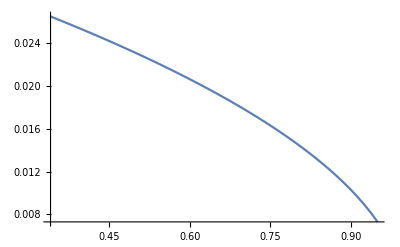

```mathematica
Plot[gzp[brin],{brin,0.34,0.95}]
```

```mathematica
gzp[0.34]
```

0.0265283

```mathematica
Sqrt[10.]
```

3.16228

```mathematica
%*0.026528336875957473
```

0.08389

```mathematica
%^2
```

0.0000703753

```mathematica
Sqrt[(5.01093)^2+1.87087/2*(0.246)^2]
```

5.01658

```mathematica
Sqrt[(5.016575350710881^2-0.46398^2)/(2.29661^2-0.46398^2)]
```

2.22077

0.677954

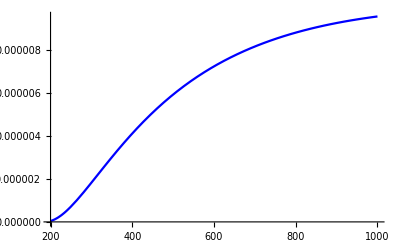

```mathematica
Sqrt[0.658273^2+(1.06436-0.19521)/2*(0.246)^2]
```